```mathematica
(*I = Is*(Exp(VD/(n*VT))-1)
I.... proud procházející diodou
   VD... napětí na diodě
	 Is... závěrný saturační proud
	   VT... tepelné napětí
		 n.... činitel kvality
n~1
VT=(k*T)/q
	k=1.38*10^23 JK^-1... Boltzmannova konst.
  q=1.6*10^-19 C... Náboj e^-
 T ...pokojová teplota (pokojová T~300K)
 *)
```

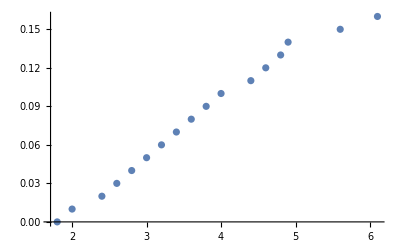

```mathematica
U ={1.8, 2.0, 2.4, 2.6, 2.8, 3.0, 3.2, 3.4, 3.6, 3.8, 4.0, 4.4, 4.6, 4.8, 4.9, 5.6, 6.1};
i = {0, 0.01, 0.02, 0.03, 0.04, 0.05, 0.06, 0.07, 0.08, 0.09, 0.10, 0.11, 0.12, 0.13, 0.14, 0.15, 0.16};

ListPlot[Table[{U[[j]], i[[j]]},{j, 17}]]
```